# Linearly Constrained GEV

The basic idea is that if I want so solve 
	M_0.v=λ M_1.v
with G.v=0 then I can build the expanded GEV
	(M_0 | Gᵀ
G | 0).(v
μ)=λ(M_1 | 0
0 | 0).(v
μ)
and just grab the bits I want.

Slightly different I can put the bits on the other side.
	(M_0 | 0
0 | 0).(v
μ)=λ(M_1 | Gᵀ
G | 0).(v
μ)
	
Since I am forcing G.v=0 I can add stuff like  X.G to the upper diagonal block occupied by M_0.  The obvious thing is to try Gᵀ.G but I could also draw a random X of the appropriate dimension
	(M_0+Gᵀ.G | Gᵀ
G | 0).(v
μ)=λ(M_1 | 0
0 | 0).(v
μ)

Looks fine.

```mathematica
(* Ambient dimension m and c constraints *)
{m,c}={12,3};
(* Build Constraint Matrix *)
(* Compute orth basis for null space *)
G=RandomReal[{-1,1}, {c,m}];
NG=NullSpace[G]ᵀ;
Map[Norm,{G.NG,NGᵀ.NG-IdentityMatrix[m-c]}]
(* Build symmetric test matrices *)
{M0,M1}=RandomReal[{-1,1},{2,m,m}];
{M0,M1}=Map[(#+#ᵀ)&,{M0,M1}];
(* Compute evals two ways *)
(* Projected and Embedded *)
{Pλs,Pvs}=Chop[Eigensystem[{NGᵀ.M0.NG,NGᵀ.M1.NG}]];
ZeroCxC=SparseArray[{},{c,c}];
{Eλs,Evs}=Chop[Eigensystem[{M0Hat,M1Hat}=Map[ArrayFlatten,{({{M0, Gᵀ}, {G, 0}}),({{M1, 0}, {0, ZeroCxC}})}]]];
TableForm[Map[Sort,{Pλs,Select[Eλs,Abs[#]<∞&]}]ᵀ,
TableHeadings->{Automatic,{"Projected","Embedded"}}]
```

{7.25773×10^-16,3.82986×10^-16}

| Projected | Embedded
1 | -3.14296-8.80264 ⅈ | -3.14296+8.80264 ⅈ
2 | -3.14296+8.80264 ⅈ | -3.14296-8.80264 ⅈ
3 | -2.75829 | -2.75829
4 | -1.13898 | -1.13898
5 | -0.585759 | -0.585759
6 | 0.369809-0.949174 ⅈ | 0.369809-0.949174 ⅈ
7 | 0.369809+0.949174 ⅈ | 0.369809+0.949174 ⅈ
8 | 0.539077 | 0.539077
9 | 5.05866 | 5.05866

```mathematica
Map[Det,{M0Hat,M1Hat}]
```

{22250.,0.}

Other way

```mathematica
(* Ambient dimension m and c constraints *)
{m,c}={12,3};
(* Build Constraint Matrix *)
(* Compute orth basis for null space *)
G=RandomReal[{-1,1}, {c,m}];
NG=NullSpace[G]ᵀ;
Map[Norm,{G.NG,NGᵀ.NG-IdentityMatrix[m-c]}]
(* Build symmetric test matrices *)
{M0,M1}=RandomReal[{-1,1},{2,m,m}];
{M0,M1}=Map[(#+#ᵀ)&,{M0,M1}];
(* Compute evals two ways *)
(* Projected and Embedded *)
{Pλs,Pvs}=Chop[Eigensystem[{NGᵀ.M0.NG,NGᵀ.M1.NG}]];
ZeroCxC=SparseArray[{},{c,c}];
Tol=10^(-7);
{Eλs,Evs}=Chop[Eigensystem[{M0Hat,M1Hat}=Map[ArrayFlatten,{({{M0, 0}, {0, ZeroCxC}}),({{M1, Gᵀ}, {G, 0}})}]]];
TableForm[Map[Sort,{Pλs,Select[Eλs,Abs[#]>Tol&]}]ᵀ,
TableHeadings->{Automatic,{"Projected","Embedded"}}]
```

{7.76404×10^-16,3.19341×10^-16}

| Projected | Embedded
1 | -5.6391 | -5.6391
2 | -0.713931 | -0.713931
3 | -0.0418914-0.209458 ⅈ | -0.0418914-0.209458 ⅈ
4 | -0.0418914+0.209458 ⅈ | -0.0418914+0.209458 ⅈ
5 | 0.444548-0.754765 ⅈ | 0.444548-0.754765 ⅈ
6 | 0.444548+0.754765 ⅈ | 0.444548+0.754765 ⅈ
7 | 0.687123 | 0.687123
8 | 1.12295 | 1.12295
9 | 1.87441 | 1.87441

Once more with feeling.

Other way

```mathematica
(* Ambient dimension m and c constraints *)
{m,c}={12,3};
(* Build Constraint Matrix *)
(* Compute orth basis for null space *)
G=RandomReal[{-1,1}, {c,m}];
NG=NullSpace[G]ᵀ;
Map[Norm,{G.NG,NGᵀ.NG-IdentityMatrix[m-c]}];
(* Build symmetric test matrices *)
{M0,M1}=RandomReal[{-1,1},{2,m,m}];
{M0,M1}=Map[(#+#ᵀ)&,{M0,M1}];
(* Compute evals two ways *)
(* Projected and Embedded *)
{Pλs,Pvs}=Chop[Eigensystem[{NGᵀ.M0.NG,NGᵀ.M1.NG}]];
ZeroCxC=SparseArray[{},{c,c}];
Tol=10^(-7);
η=RandomReal[{0.1,1}];
{Eλs,Evs}=Chop[Eigensystem[{M0Hat,M1Hat}=Map[ArrayFlatten,{({{M0+η Gᵀ.G, 0}, {0, ZeroCxC}}),({{M1, Gᵀ}, {G, 0}})}]]];
TableForm[Map[Sort,{Pλs,Select[Eλs,Abs[#]>Tol&]}]ᵀ,
TableHeadings->{Automatic,{"Projected","Embedded"}}]
```

| Projected | Embedded
1 | -1.63675 | -1.63675
2 | -0.245999-1.20613 ⅈ | -0.245999-1.20613 ⅈ
3 | -0.245999+1.20613 ⅈ | -0.245999+1.20613 ⅈ
4 | 0.319706+2.50703 ⅈ | 0.319706-2.50703 ⅈ
5 | 0.319706-2.50703 ⅈ | 0.319706+2.50703 ⅈ
6 | 0.343521+0.346215 ⅈ | 0.343521+0.346215 ⅈ
7 | 0.343521-0.346215 ⅈ | 0.343521-0.346215 ⅈ
8 | 0.625697+1.5954 ⅈ | 0.625697-1.5954 ⅈ
9 | 0.625697-1.5954 ⅈ | 0.625697+1.5954 ⅈ

```mathematica
Map[Det,{M0Hat,M1Hat}]
```

{0.,-3029.5}

# GEV Idea Test

## Rebuild and Test of TRS GEV Pencil 2n×2n

```mathematica
m=12
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1=ArrayFlatten[({{0, B}, {B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

12

| obj | cons: p.B.p-Δ^2
GEV | -1.01629 | -1.31145×10^-15
FindMin | -1.01629 | 9.9991×10^-9

Making functions.

```mathematica
TRSMatrices[A_,B_,g_,Δ_]:= Module[{},
(* M0 and M1 *)
Map[ ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),({{0, B}, {B, 0}})}]
]
TRSMin[A_,B_,g_,Δ_]:= Module[{m=Length[A],M0,M1, λs,vs,y1,y2},
{M0,M1}=TRSMatrices[A,B,g,Δ];
(* Does not treat or test the hard case *)
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
{y1,y2}=Partition[vs⟦1⟧,m];
(* This is the constrained argmin *)
-Sign[g.y2] Δ y1/(√(y1.B.y1))
]
```

Testing the function

```mathematica
{m,Δ}={12,0.2};
{A,B}=RandomReal[{-1,1},{2,m,m}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},m];
pMinGEV=TRSMin[A,B,g,Δ];
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV | -8.41813 | -2.08167×10^-17
FindMin | -8.41813 | 1.7234×10^-9

## Rebuild and Test of TRS GEV Pencil (2n+1)×(2n+1)

```mathematica
m=14;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
Δ=0.2;
M0 = ArrayFlatten[({{Δ^2, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
λPick=1;
y1y2=Drop[vs⟦λPick⟧,1];
{y1,y2}=Partition[y1y2,m];
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV | -1.36797 | -2.22045×10^-16
FindMin | -1.36797 | 9.99957×10^-9

Making functions.

```mathematica
TRSMatricesBig[A_,B_,g_,Δ_]:= Module[{},
(* M0 and M1 *)
Map[ ArrayFlatten,{({{Δ^2, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}}),({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})}]
]
TRSMinBig[A_,B_,g_,Δ_]:= Module[{m=Length[A],M0,M1, λs,vs,y1,y2,λPick},
{M0,M1}=TRSMatricesBig[A,B,g,Δ];
(* Does not treat or test the hard case *)
{λs,vs} =Sort[Chop[Eigensystem[{M0,M1}]]ᵀ]ᵀ;
(* The ComplexInfinity eigenvalues sorst to the back! *)
(* We want the first eigenvector *)
λPick=1;
(* The bits to build p from y1 and y2 are at the back *)
{y1,y2}=Partition[Drop[vs⟦λPick⟧,1],m];
(* This is the constrained argmin *)
-Sign[g.y2] Δ y1/(√(y1.B.y1))
]
```

Testing the function

```mathematica
{m,Δ}={12,0.2};
{A,B}=RandomReal[{-1,1},{2,m,m}];{A,B}={A+Aᵀ,B.Bᵀ};
g=RandomReal[{-1,1},m];
pMinGEV=TRSMin[A,B,g,Δ];
pMinGEVBig=TRSMinBig[A,B,g,Δ];
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ] ;
pMinFM=vars/.FMinSub;
TableForm[{
{FullForm[f[p]],Cons[p]}/.p->pMinGEV,
{FullForm[f[p]],Cons[p]}/.p->pMinGEVBig,
{FullForm[f[p]],Cons[p]}/.p->pMinFM},
TableHeadings->{{"GEV Small","GEV Big","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2
GEV Small | -0.787563 | -1.80411×10^-16
GEV Big | -0.787563 | -9.02056×10^-17
FindMin | -0.787563 | -3.0994×10^-9

## KKT Matrix with Equality Constraints

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
Map[Norm,{G.p,A.p+Gᵀ.μ-g}]
```

{6.50334×10^-16,1.50393×10^-15}

The solution does not depend on the “size” of G.  I get exactly the same answer if I scale G→ϵ G. The p stays the same.  The multipliers μ get scaled by 1/ϵ.  If I make the scaling too small I will get warnings from the condition number estimator.

```mathematica
{m,c}={13,3};
{A,G}=Map[RandomReal[{-1,1},{#,m}]&,{m,c}]; A=A+Aᵀ;
g=RandomReal[{-1,1},m];
KKT=ArrayFlatten[({{A, Gᵀ}, {G, 0}})];
pμ=LinearSolve[KKT,Join[g,ConstantArray[0,c]]];
{p,μ}={pμ⟦1;;m⟧,Drop[pμ,m]};
ϵ=0.001;
KKT1=ArrayFlatten[({{A, ϵ Gᵀ}, {ϵ G, 0}})];
pμ1=LinearSolve[KKT1,Join[g,ConstantArray[0,c]]];
{p1,μ1}={pμ1⟦1;;m⟧,Drop[pμ1,m]};
Map[Norm,{p-p1,μ-ϵ μ1}]
```

{7.14189×10^-15,2.28056×10^-15}

Minimizing p.A.p is basically the same as minimizing (p | μ).(A | ϵ Gᵀ
ϵ G | 0).(p
μ) when ϵ is small and G.p is small.  The plan is to use the scaled KKT matrix in the objective with the extended trust region matrix  (B | 0
0 | γ Ic) for a small γ.  Essentially as γ goes to zero we are turning off the penalization on the multiplier μ.

## Extend and Test of TRS GEV Pencil

I can enforce the constraint G.p=0 and incorporate the multiplier term Gᵀ.μ by adding the extra blocks.  I am going to do this for the small envelope first.

### Small Envelope

Padding on the natural ∞ side!  This is a singular pencil!

```mathematica
{m,c}={4,2};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
(* Build the unconstrained matrices *)
(* Currently as dense *)
(* Insert TRS GEV matrices *)
{M0Pad,M1Pad}=ConstantArray[0,{2,2m+c,2m+c}];
{M0,M1}=TRSMatrices[A,B,g,Δ];
{M0Pad⟦1;;2m,1;;2m⟧,M1Pad⟦1;;2m,1;;2m⟧}={M0,M1};
(* Insert equality constraint matrices *) 
M0Pad⟦1;;m,2m+1;;2m+c⟧=Gᵀ;
M0Pad⟦2m+1;;2m+c, 1;;m⟧=G;
(* Check Singularity *)
Map[Det,{M0Pad,M1Pad}]
(* Crap *)
```

{2.98439×10^-15,0.}

Pad on the other side!  This is also a singular pencil.

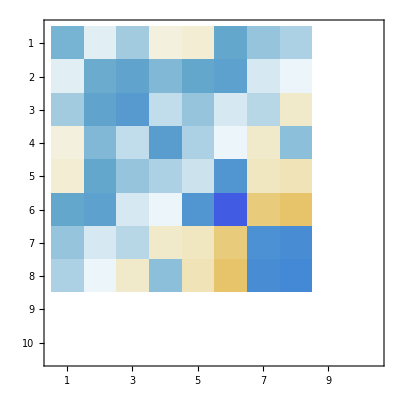
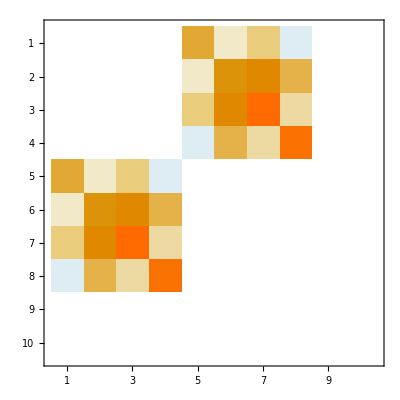

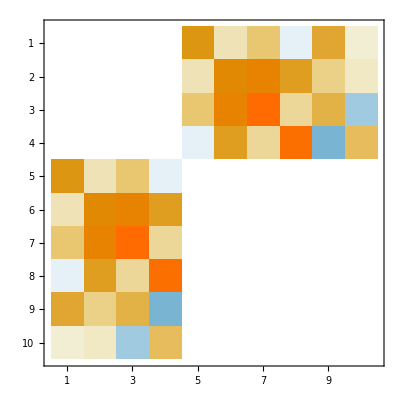
{-Graphics-,-Graphics-}

```mathematica
{m,c}={4,2};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
(* Build the unconstrained matrices *)
(* Currently as dense *)
(* Insert TRS GEV matrices *)
{M0Pad,M1Pad}=ConstantArray[0,{2,2m+c,2m+c}];
{M0,M1}=TRSMatrices[A,B,g,Δ];
{M0Pad⟦1;;2m,1;;2m⟧,M1Pad⟦1;;2m,1;;2m⟧}={M0,M1};
Map[MatrixPlot,{M0Pad,M1Pad}]
(* Insert equality constraint matrices *) 
M1Pad⟦1;;m,2m+1;;2m+c⟧=Gᵀ;
M1Pad⟦2m+1;;2m+c, 1;;m⟧=G;
Map[MatrixPlot,{M0Pad,M1Pad}]
(* Check Singularity *)
Map[Det,{M0Pad,M1Pad}]
(* Crap *)
```

Add the M0 perturbation

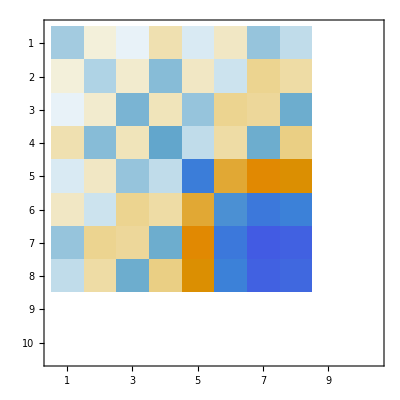
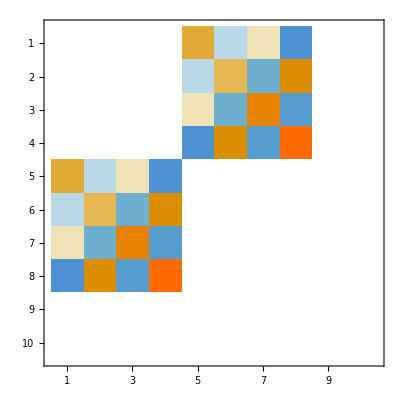

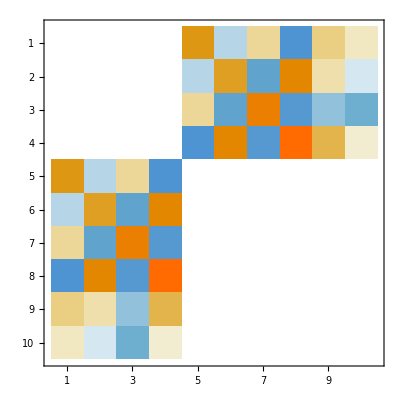
{-Graphics-,-Graphics-}

{0.,0.}

```mathematica
{m,c}={4,2};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
(* Build the unconstrained matrices *)
(* Currently as dense *)
(* Insert TRS GEV matrices *)
{M0Pad,M1Pad}=ConstantArray[0,{2,2m+c,2m+c}];
{M0,M1}=TRSMatrices[A+η Gᵀ.G,B,g,Δ];
η=RandomReal[{0.1,1}];
{M0Pad⟦1;;2m,1;;2m⟧,M1Pad⟦1;;2m,1;;2m⟧}={M0,M1};
Map[MatrixPlot,{M0Pad,M1Pad}]
(* Insert equality constraint matrices *) 
M1Pad⟦1;;m,2m+1;;2m+c⟧=Gᵀ;
M1Pad⟦2m+1;;2m+c, 1;;m⟧=G;
Map[MatrixPlot,{M0Pad,M1Pad}]
(* Check Singularity *)
Map[Det,{M0Pad,M1Pad}]
(* Crap *)
```

### Big Envelope

```mathematica
{m,c}={12,2};
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
g=RandomReal[{-1,1},m];
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
G=RandomReal[{-1,1},{c,m}];
Δ=0.2;
(* Build the unconstrained matrices *)
{M0Big,M1Big}=TRSMatricesBig[A,B,g,Δ];
(* Initialize the expanded Equality Constrained Matrices *)
(*M0Eq=M1Eq=SparseArray[{},{2m+1+c,2m+1+c}];*)
(* Dense for testing *)
M0Eq=M1Eq=ConstantArray[0,{2m+1+c,2m+1+c}];
(* Copy the old bits in *)
M0Eq⟦1;;2m+1,1;;2m+1⟧=M0Big;
M1Eq⟦1;;2m+1,1;;2m+1⟧=M1Big;
Map[MatrixPlot,{M0Eq,M1Eq}];
(* Add the new bits *)
M0Eq⟦1+2m+1;;1+2m+c,2;;m+1⟧=G;
M0Eq⟦2;;m+1,1+2m+1;;1+2m+c⟧=Gᵀ;
(* Try a regularization ϵ*)
ϵ=0.0 1.0*10^-12;
M1Eq⟦-c;;-1,-c;;-1⟧=ϵ IdentityMatrix[c];
(* Compute reference solution using FindMin *)
Clear[f,Cons,x,p]
f[p_]:= 0.5 p.A.p + g.p
Cons[p_]:=p.B.p-Δ^2 
{vars,vars0}={Array[x,m],RandomReal[{-1,1},m]};
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,{vars.B.vars<=Δ^2,G.vars==ConstantArray[0,c]}},{vars, vars0}ᵀ] ;
pMinFMEq=vars/.FMinSub;
(* Test new code *)
{λs,vs} =Sort[Chop[Eigensystem[{M0Eq,M1Eq}]]ᵀ]ᵀ;
(* The ComplexInfinity eigenvalues sorst to the back! *)
(* We want the first eigenvector *)
MatrixPlot[vs,Mesh->All];
λPick=1;
Print[λs⟦λPick⟧];
y1y2μ=Drop[vs⟦λPick⟧,1];
{{y1,y2},μ}={Partition[y1y2μ⟦1;;2m⟧,m],Drop[y1y2μ,1m]};
pMinGEVEq=-Sign[g.y2] Δ y1/(√(y1.B.y1));
(* compare answers *)
TableForm[{
{FullForm[f[p]],Cons[p],G.p}/.p->pMinFMEq,
{FullForm[f[p]],Cons[p],G.p}/.p->pMinGEVEq
},
TableHeadings->{{"FindMin","GEV+"},{"obj","cons: p.B.p-Δ^2","cons: G.p"}}]
```

-8.95026-14.7574 ⅈ

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

| obj | cons: p.B.p-Δ^2 | cons: G.p
FindMin | -0.321302 | -1.03307×10^-8 | -1.64799×10^-16
4.85723×10^-17
GEV+ | Indeterminate | Indeterminate | Indeterminate
Indeterminate

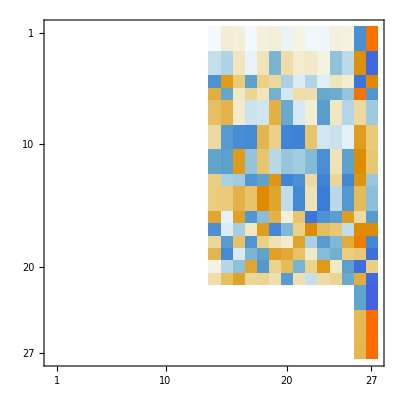

```mathematica
MatrixPlot[vs]
```

```mathematica
M0Big = ArrayFlatten[({{□, □, 0}, {□, □, 0}, {0, 0, ConstantArray[0,{c,c}]}})];
M1Big=ArrayFlatten[({{0, B, Gᵀ}, {B, 0, 0}, {G, 0, 0}})];
{λs,vs} =Sort[Chop[Eigensystem[{M0Big,M1Big}]]ᵀ]ᵀ;
λs
```

{-3.83599,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,-0.146844+5.33786 ⅈ,-0.146844-5.33786 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248,-2.37648×10^-8,2.37648×10^-8,0.159302-0.0313006 ⅈ,0.159302+0.0313006 ⅈ,0.204316-0.196461 ⅈ,0.204316+0.196461 ⅈ,0.256525,0.805966,1.29504,1.72635,2.75087,ComplexInfinity,ComplexInfinity}

```mathematica
{y1,y2}=Partition[vs⟦1,1;;2m⟧,m];λ=vs⟦1,2m+1;;-1⟧;
Map[Dimensions,{y1,y2,λ}]
```

{{12},{12},{3}}

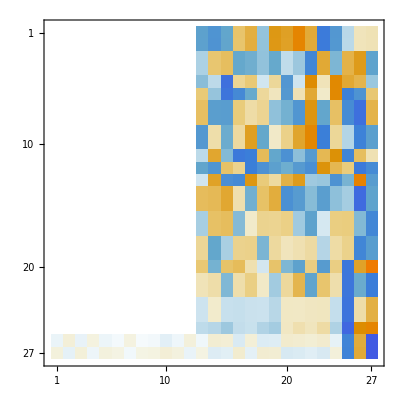

{ComplexInfinity,ComplexInfinity,-0.146844-5.33786 ⅈ,-0.146844+5.33786 ⅈ,-3.83599+0. ⅈ,2.75087+0. ⅈ,-1.13095-2.30659 ⅈ,-1.13095+2.30659 ⅈ,-2.0191+0.224868 ⅈ,-2.0191-0.224868 ⅈ,1.72635+0. ⅈ,1.29504+0. ⅈ,0.805966+0. ⅈ,-0.418531-0.0842568 ⅈ,-0.418531+0.0842568 ⅈ,-0.323511+0.229454 ⅈ,-0.323511-0.229454 ⅈ,0.204316+0.196461 ⅈ,0.204316-0.196461 ⅈ,0.256525+0. ⅈ,0.159302+0.0313006 ⅈ,0.159302-0.0313006 ⅈ,-0.08791-0.0271893 ⅈ,-0.08791+0.0271893 ⅈ,-0.0665248+0. ⅈ,2.3765×10^-8+0. ⅈ,-2.3765×10^-8+0. ⅈ}

```mathematica
MatrixPlot[NewV=Chop[Eigenvectors[{M0Big,M1Big}]]]
vv=NewV⟦-1⟧;
p1=vv⟦1;;m⟧;
Eigenvalues[{M0Big,M1Big}]
```

```mathematica
pMinGEV=-Sign[g.y2] Δ y1/(√(y1.B.y1));
f[p_]:= 0.5 p.A.p + g.p
ECons[p_]:=p.B.p-Δ^2
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
vars=Array[x,m];
vars0=RandomReal[{-1,1},m];
{FMVal,FMinSub}=FindMinimum[{0.5 vars.A.vars + g.vars,vars.B.vars<=Δ^2},{vars, vars0}ᵀ,PrecisionGoal->10] ;
pMinFM=vars/.FMinSub;
TableForm[{{FullForm[f[p]],ECons[p],G.p}/.p->pMinGEV,
{FullForm[f[p]],ECons[p]}/.p->pMinFM},
TableHeadings->{{"GEV","FindMin"},{"obj","cons: p.B.p-Δ^2"}}]
```

| obj | cons: p.B.p-Δ^2 | 
GEV | -0.00377929 | -6.93889×10^-18 | -0.0704259
0.0940681
0.147426
FindMin | -0.281915 | 9.99791×10^-9 |

```mathematica
?Partition
```